```mathematica
Clear["Global`*"]
```

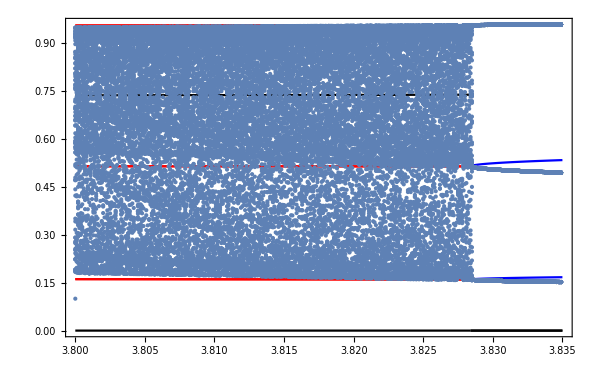

```mathematica
listpointsxy={}
listpointsxμT = {}
(* valores de mu na lista total*)
For[μ = 3.8, μ<3.8284,μ=μ+0.0001;
listpointsxμlocal = {};
x = 0.99;
y =1. 10^-10;
AppendTo[listpointsxy,{x, y}];
(* definicao do n de iteracoes *)
if=50000;
For[i=1,i<if,i++,
(* condicao de estabilidade *)
If[x^2+y^2≤ 1,
(* processo de iteracao *)
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x, y}];
(* condicao para reduzir valores *)
If[y^2<10^-10,
(* adicao dos valores de x para um unico mu a uma lista *)
AppendTo[listpointsxμlocal,x],
Null],
i=if]];
(* adicao das listas contendo os valores de x para diferentes mu's em uma unica lista *)
AppendTo[listpointsxμT, listpointsxμlocal]]
```

{}

{}

General::munfl: (2.79427×10^-78)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.12631×10^-78)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.80422×10^-78)^4 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
.
```

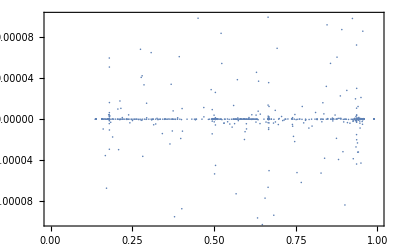

```mathematica
ListPlot[listpointsxy,PlotRange->{{0,1},{-10^-4,10^-4}},Frame->True]
```

```mathematica
Length[listpointsxy]
```

50864

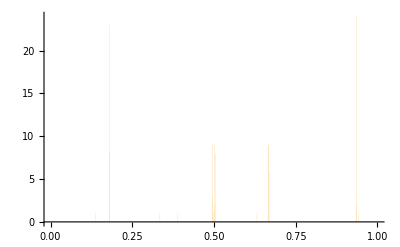
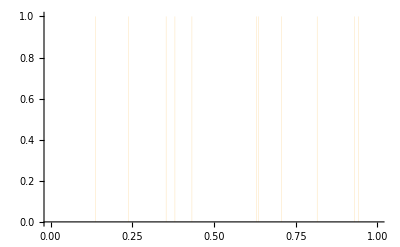
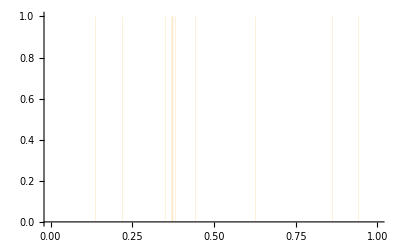
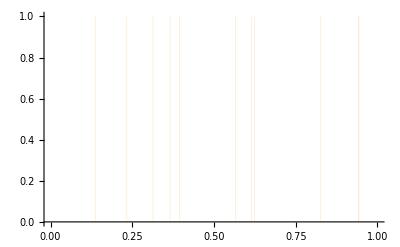
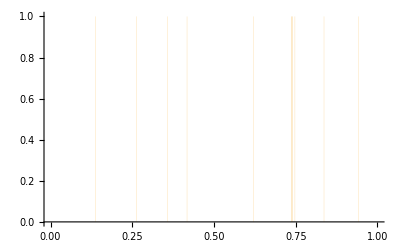
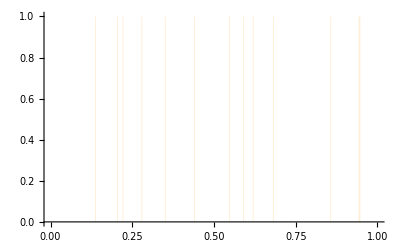
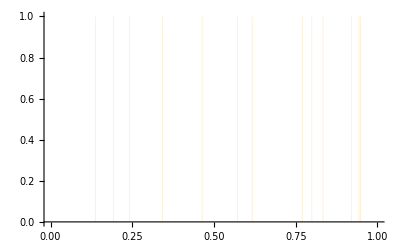
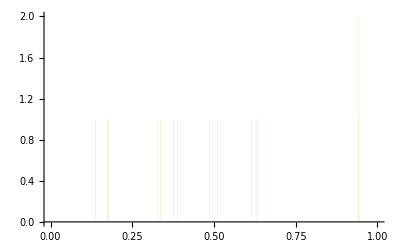

```mathematica
Table[Histogram[{Flatten[listpointsxμT⟦i⟧]},{0,1,10^-3}],{i,1,29}]
```

```mathematica
listpointsxy={};
listpointsxμTIndex = {};
listpointsxμT = {};
For[μ = 3.820, μ<3.830,μ=μ+0.0001;
listpointsxμlocal = {};
AppendTo[listpointsxμlocal, μ];
(* valores de 0 a 1 a serem testados para x*)

For[j=2,j< 3 10^1,j++,
x=(j-1)1/(3 10^1);
For[k=-1,k≤ 1,k++,
y = k 10^-1;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
if=500;
(* definicao do n de iteracoes *)
For[i=1,i<if,i++,
(* condicao de estabilidade *)
If[x^2+y^2≤ 1,
(* processo de iteracao *)
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x,α y,0}];
(* condicao para reduzir valores *)
If[y^2<10^-12,
(* adicao dos valores de x para um unico mu a uma lista *)
AppendTo[listpointsxμlocal,{x}],
Null],
i=if]]]];
(* adicao das listas contendo os valores de x para diferentes mu's em uma unica lista *)
AppendTo[listpointsxμTIndex, Flatten[listpointsxμlocal]]]

For[i = 0, i <Length[listpointsxμTIndex], i++;
local = Delete[listpointsxμTIndex⟦i⟧,1];
AppendTo[listpointsxμT,local]]
```

$Aborted

```mathematica
x = 0.1;
listpoints = {};
j=1;
For[μ = 3.8, μ<3.83,μ=μ+0.000001,
For[i=1,i<100,i++,
x = μ x(1-x)
];
AppendTo[listpoints,{μ}];
For[i=1,i<15,i++,
x =μ x(1-x);
AppendTo[listpoints⟦j⟧,x];
];
j++;
]
```

```mathematica
ListPlot[TemporalData[listpoints⟦All,2;;⟧,{listpoints⟦All,1⟧}],PlotStyle->Directive[RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.00001]],Frame->True]
```

-Graphics-

```mathematica
x = 0.1;
listpoints = {};
j=1;
For[μ = 3.8, μ<3.83,μ=μ+0.001,
For[i=1,i<100,i++,
x = μ x(1-x)
];
AppendTo[listpoints,{μ}];
For[i=1,i<3,i++,
x =μ x(1-x);
AppendTo[listpoints⟦j⟧,x];
];
j++;
]
```

```mathematica
listpoints
```

{{3.8,0.420198,0.9258},{3.801,0.845772,0.49581},{3.802,0.427873,0.930721},{3.803,0.396194,0.90977},{3.804,0.204697,0.619277},{3.805,0.382875,0.899052},{3.806,0.85559,0.470254},{3.807,0.890356,0.371647},{3.808,0.850597,0.483928},{3.809,0.920653,0.278252},{3.81,0.634888,0.883178},{3.811,0.945871,0.19512},{3.812,0.659914,0.855518},{3.813,0.767342,0.680728},{3.814,0.926481,0.259787},{3.815,0.826185,0.547848},{3.816,0.249744,0.715012},{3.817,0.930534,0.246732},{3.818,0.914367,0.298948},{3.819,0.597973,0.918093},{3.82,0.879891,0.403709},{3.821,0.944927,0.198846},{3.822,0.368929,0.889839},{3.823,0.954431,0.166271},{3.824,0.24044,0.698373},{3.825,0.945096,0.198478},{3.826,0.189525,0.587693},{3.827,0.954457,0.166356},{3.828,0.955164,0.163938},{3.829,0.956973,0.157663}}

```mathematica
ListDensityPlot[TemporalData[listpoints⟦All,2;;⟧,{listpoints⟦All,1⟧}]]
```

ListDensityPlot::arrayerr: … must be a valid array.

ListDensityPlot[TemporalData[…]]

```mathematica
Length[listpointsxμTIndex⟦1⟧] - Length[listpointsxμT⟦1⟧]
```

1

```mathematica
Length[listpointsxy]
```

56201

```mathematica
Length[listpointsxμT]
```

20

Part::partw: Part 36 of {{3.8,0.855137,0.470736},{3.801,0.190793,0.586841},{3.802,0.273978,0.756271},{3.803,0.797124,0.615012},«27»,{3.831,0.941184,0.212073},{3.832,0.882549,0.39721},{3.833,0.28933,0.788135},{3.834,0.883145,0.39567}} does not exist.

Part::partw: Part 37 of {{3.8,0.855137,0.470736},{3.801,0.190793,0.586841},{3.802,0.273978,0.756271},{3.803,0.797124,0.615012},«27»,{3.831,0.941184,0.212073},{3.832,0.882549,0.39721},{3.833,0.28933,0.788135},{3.834,0.883145,0.39567}} does not exist.

Part::partw: Part 38 of {{3.8,0.855137,0.470736},{3.801,0.190793,0.586841},{3.802,0.273978,0.756271},{3.803,0.797124,0.615012},«27»,{3.831,0.941184,0.212073},{3.832,0.882549,0.39721},{3.833,0.28933,0.788135},{3.834,0.883145,0.39567}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

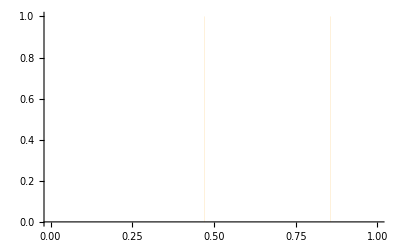
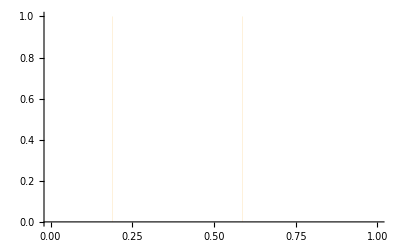
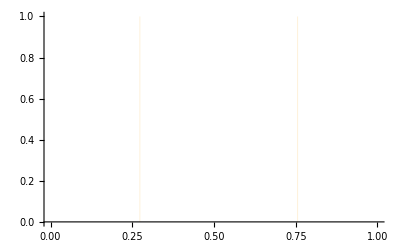
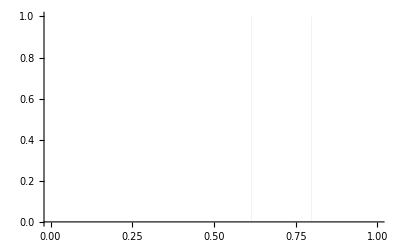
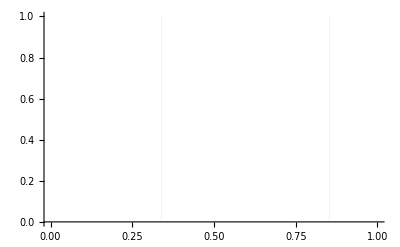
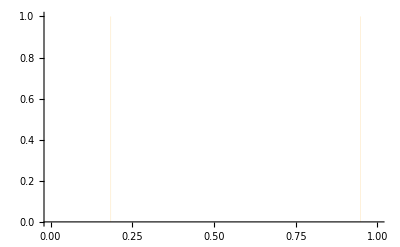
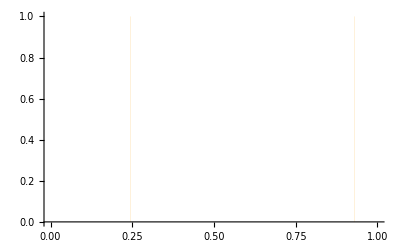
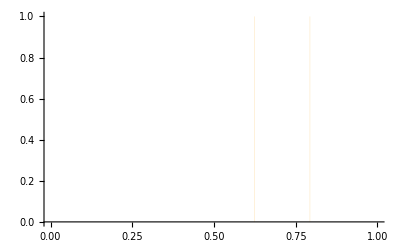
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HisT=Table[Histogram[{Flatten[listpoints⟦i⟧]},{0,1,10^-3}],{i,1,Length[listpointsxμT]}]
```

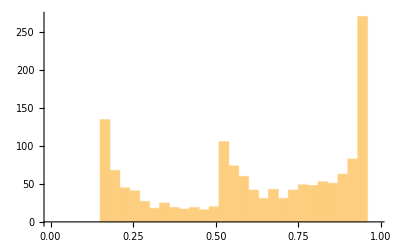

```mathematica
h =Histogram[Flatten[listpointsxμT⟦10⟧],{0,1,3 10^-2}]
```

```mathematica
HL=HistogramList[listpointsxμT⟦15⟧,{0,1,3 10^-2}]
```

{{0,3/100,3/50,9/100,3/25,3/20,9/50,21/100,6/25,27/100,3/10,33/100,9/25,39/100,21/50,9/20,12/25,51/100,27/50,57/100,3/5,63/100,33/50,69/100,18/25,3/4,39/50,81/100,21/25,87/100,9/10,93/100,24/25,99/100},{0,0,0,0,0,207,58,28,27,24,26,20,17,8,17,17,19,176,52,48,48,25,30,29,45,37,38,33,40,52,73,303,0}}

```mathematica
gaus3[xn_]=A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2];
```

O código abaixo não é relevante para os objetivos atuais, fiz ele apenas por confusão. Mas acho que pode vir a ser útil dependendo dos problemas que vamos encontrar.

```mathematica
(*cuttingvalues1 ={};
cuttingvalues2 ={};
flatlist = Sort[{Flatten[listpointsxμT⟦25⟧]}];
For[i=0,i≤ Length[flatlist⟦1⟧] - 1,i++;
j = flatlist⟦1,i⟧;
If[0.305> j>0.3,AppendTo[cuttingvalues1,i],j];
If[0.805> j>0.8,AppendTo[cuttingvalues2,i],j]]

cut1 = Min[cuttingvalues1];
cut2 = Min[cuttingvalues2];

flatlist1 = flatlist[[;;cut1]];
flatlistlocal = flatlist[[cut1;;]];
flatlist2 = flatlistlocal[[;;cut3]];
flatlist3 = flatlistlocal[[cut3;;]];*)
```

pointshl -->  Lista com os pontos mais altos de cada coluna do histograma no formato {{ x1, y1 }, { x2, y2 }, ... }
peaks --> O FindPeaks foi usado para encontrar os picos do histograma. O fator σ  =  2  foi suficiente para isolar os 3 picos desejados.
indexes -->  Lista com os índices de cada pico
Finalmente igualamos {x1, x2, x3} aos valores encontrados para os picos.

```mathematica
pointshl =Partition[Riffle[HL⟦1⟧,HL⟦2⟧],2];
peaks  = FindPeaks[HL⟦2⟧,2];
indexes = peaks[[All,1]]
{x1,x2,x3} = {HL⟦1,indexes⟦1⟧⟧,HL⟦1,indexes⟦2⟧⟧,HL⟦1,indexes⟦3⟧⟧}
```

{6,18,32}

{3/20,51/100,93/100}

Finalmente, tentativa de usar NonlinearModelFit para encontrar os coeficientes desejados. 
Falha na convergência.

Como proceder?

FittedModel[-38.7245 ⅇ^(-7.77519 (-93/100+xn)^2)+27.9623 ⅇ^(-4.54274 ((«1»«1»)^2)+15.2686 ⅇ^(3.48679 (-3/20+xn)^2)]

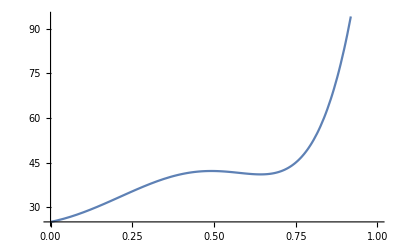

```mathematica
nlm=NonlinearModelFit[pointshl,A1 Exp[β1 (xn-x1)^2]+A2 Exp[β2(xn-x2)^2]+A3 Exp[β3(xn-x3)^2],{A1,A2,A3,β1,β2,β3 },xn]
Plot[nlm[x],{x,0,1}]
```

```mathematica
x1
Clear[α]
```

3/20

{A1→206.967,A2→175.633,A3→302.967,α1→-2177.68,α2→-1740.41,α3→-2345.86}

General::munfl: Exp[-2028.84] is too small to represent as a normalized machine number; precision may be lost.

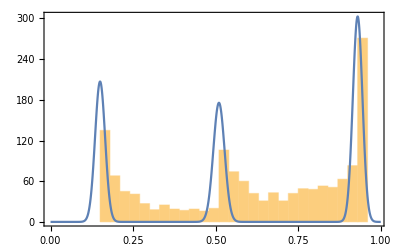

```mathematica
fitgaussian = FindFit[pointshl,{A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2], {α1<-10^3,α2<-10^3,α3<-10^3,A1>0,A2>0,A3>0}},{A1,A2,A3, α1,α2,α3},xn]
Show[h ,Plot[(A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2])/.fitgaussian,{xn,0,1},PlotRange->All],Frame-> True]
```

{A1→195.796,A2→175.566,A3→297.41,A4→52.5085,A5→33.0893,α1→-2735.42,α2→-1747.13,α3→-2576.82,α4→-100.,α5→-100.,x4→0.780284,x5→0.254063}

General::munfl: Exp[-2228.6] is too small to represent as a normalized machine number; precision may be lost.

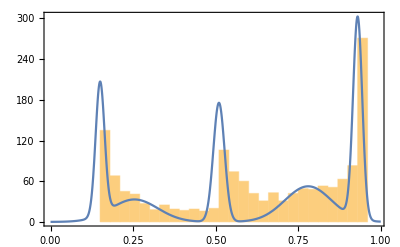

```mathematica
fitgaussian = FindFit[pointshl,{A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2], {α1<-10^3,α2<-10^3,α3<-10^3,α4<-10^2,α5<-10^2,A1>0,A2>0,A3>0,A4>0,A5>0,x2<x4<x3,x1<x5<x2}},{A1,A2,A3,A4, A5,α1,α2,α3,α4,α5,x4,x5},xn]
Show[h ,Plot[(A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2])/.fitgaussian,{xn,0,1},PlotRange->All],Frame-> True]
```

Apesar de parecer interessante, o SmoothHistogram apresenta resultados abruptamente diferentes ao alterar o fator da função de 0.6994 para 0.6995
Não resulta muito bem na curva que queríamos.

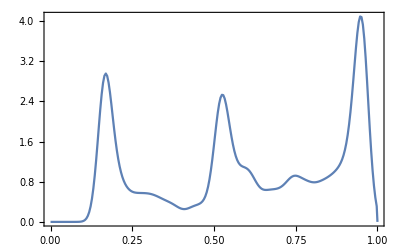

```mathematica
SmoothHistogram[Flatten[listpointsxμT⟦15⟧],0.02, "PDF", PlotRange->{{0,1},Automatic},Frame->True,PlotRange->{0,3}]
```

Em compensação, uma mera interpolação do conjunto de pontos mais altos da coluna do histograma (pointshl, definido acima), foi suficiente para encontrar um comportamento satisfatório.

InterpolatingFunction[…]

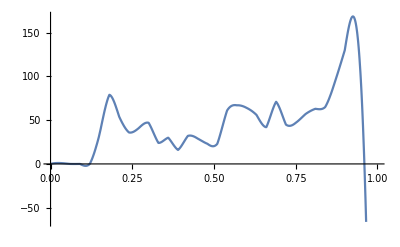

```mathematica
fhl = Interpolation[pointshl, Method->"Hermite"]
Plot[fhl[x],{x,0,1}]
```

Processo quase inteiramente automatizado, faltando somente a função das 3 gaussianas.

```mathematica
ptslencol = {}
For[ i=0, i< Length[listpointsxμT], i++;
HLlocal=HistogramList[Flatten[listpointsxμT⟦i⟧],{0,1,3 10^-2}];
pointshllocal =Partition[Riffle[HLlocal⟦1⟧,HLlocal⟦2⟧],2];
peakslocal  = FindPeaks[HLlocal⟦2⟧,2];
indexeslocal = peakslocal[[All,1]];
{x1l,x2l,x3l} = {HLlocal⟦1,indexes⟦1⟧⟧,HLlocal⟦1,indexes⟦2⟧⟧,HL⟦1,indexes⟦3⟧⟧};
fhllocal = Interpolation[pointshl];
nlmlocal= 0;
fproduto = fhllocal - nlmlocal;
peaksfinal = FindPeaks[fproduto,2];
indexesfinal = peaksfinal[[All,1]];
{x4l,x5l} = {HLlocal⟦1,indexesfinal⟦1⟧⟧,HLlocal⟦1,indexesfinal⟦2⟧⟧};
AppendTo[ptslencol,{x1l,x2l,x3l,x4l,x5l}]]
```

Do que foi proposto, eu consegui apenas:
-  Encontrar x1, x2 e x3
-  Encontrar a função interpolada

O que eu não consegui:
-  Encontrar os coeficientes para gauss3

Próximos passos:
-  Com os coeficientes, fazer a subtração entre a função interpolada e gauss3. Com isso encontramos o x4 e o x5, os picos menos expressivos (para o caso particular do listpointsxμT⟦25⟧)
-  Automatizar o processo (quase pronto) a fim de fazer isso para os outros valores de μ dentro da listpointsxμT, e observar com x1, x2, x3, x4, x5 variam com μ.

```mathematica
σ =  0.9
listμpeak = {}
For[ i=0, i<Length[listpointsxμT],i++;
HLlocal = HistogramList[listpointsxμT⟦i⟧,{0,1,3 10^-2}];
peaksl  = FindPeaks[HLlocal⟦2⟧,σ];
indexesl = Round[peaksl[[All,1]]];
{x1,x2,x3} = {HLlocal⟦1,indexesl⟦1⟧⟧,HLlocal⟦1,indexesl⟦2⟧⟧,HLlocal⟦1,indexesl⟦3⟧⟧};
AppendTo[listμpeak,{listpointsxμTIndex⟦i,1⟧,x1}]]

listμpeak2 = {}
For[ i=0, i<Length[listpointsxμT],i++;
HLlocal = HistogramList[listpointsxμT⟦i⟧,{0,1,3 10^-2}];
peaksl  = FindPeaks[HLlocal⟦2⟧,σ];
indexesl = IntegerPart[peaksl[[All,1]]];
{x1,x2,x3} = {HLlocal⟦1,indexesl⟦1⟧⟧,HLlocal⟦1,indexesl⟦2⟧⟧,HLlocal⟦1,indexesl⟦3⟧⟧};
AppendTo[listμpeak2,{listpointsxμTIndex⟦i,1⟧,x2}]]

listμpeak3 = {}
For[ i=0, i<Length[listpointsxμT],i++;
HLlocal = HistogramList[listpointsxμT⟦i⟧,{0,1,3 10^-2}];
peaksl  = FindPeaks[HLlocal⟦2⟧,σ];
indexesl = IntegerPart[peaksl[[All,1]]];
{x1,x2,x3} = {HLlocal⟦1,indexesl⟦1⟧⟧,HLlocal⟦1,indexesl⟦2⟧⟧,HLlocal⟦1,indexesl⟦3⟧⟧};
AppendTo[listμpeak3,{listpointsxμTIndex⟦i,1⟧,x3}]]
```

0.9

{}

{}

{}

```mathematica
listμpeak
```

{{3.8205,9/50},{3.821,3/20},{3.8215,9/50},{3.822,3/20},{3.8225,3/20},{3.823,3/20},{3.8235,3/20},{3.824,3/20},{3.8245,3/20},{3.825,3/20},{3.8255,3/20},{3.826,3/20},{3.8265,3/20},{3.827,3/20},{3.8275,3/20},{3.828,3/20},{3.8285,3/20},{3.829,3/20},{3.8295,3/20},{3.83,3/20}}

8007.4-4184.99 z+546.822 z^2

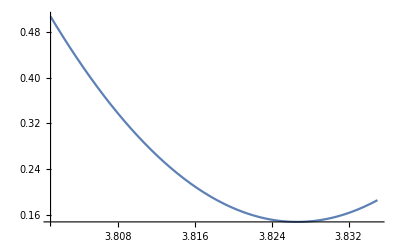

```mathematica
peakμf = Fit[listμpeak, {1,z,z^2},z]
Plot[peakμf,{z,3.801,3.835}]
```

35.5517-9.15789 z

-13.4276+3.74436 z

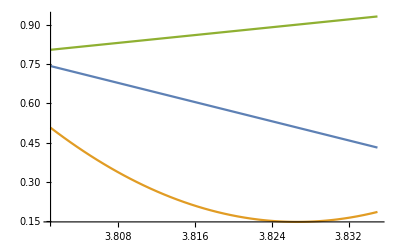

```mathematica
peakμf2 = Fit[listμpeak2,{1,z},z]
peakμf3 = Fit[listμpeak3, {1,z},z]
Plot[{peakμf2,peakμf, peakμf3},{z,3.801,3.835}, PlotRange->All]
```

```mathematica
i = 3;
HLlocal = HistogramList[listpointsxμT⟦i⟧,{0,1,3 10^-2}];
peaksl  = FindPeaks[HLlocal⟦2⟧,1.5]
indexesl = peaksl[[All,1]]
{x1,x2,x3} = {HLlocal⟦1,indexesl⟦1⟧⟧,HLlocal⟦1,indexesl⟦2⟧⟧,HLlocal⟦1,indexesl⟦3⟧⟧}
```

{{8,79},{19,70},{32,196}}

{8,19,32}

{21/100,27/50,93/100}

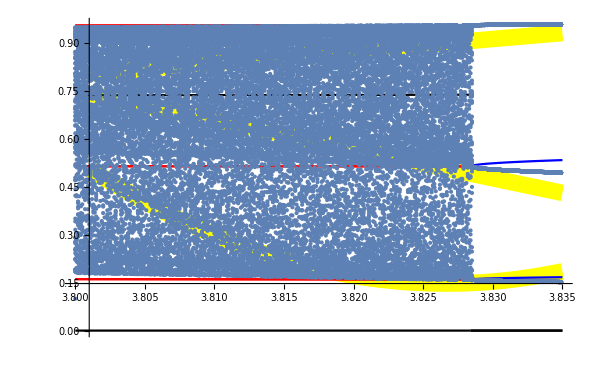

```mathematica
Show[Plot[{peakμf2,peakμf, peakμf3},{z,3.801,3.835}, PlotRange->All, PlotStyle->Directive[Thickness[0.02],Yellow]],-Graphics-]
```

```mathematica
fitL={};
For[j=1,j≤Length[listpointsxμT],j++,
HL=HistogramList[listpointsxμT⟦j⟧,{0,1,3 10^-2}];
pointshl =Partition[Riffle[HL⟦1⟧,HL⟦2⟧],2];
peaks  = FindPeaks[HL⟦2⟧,2];
indexes = peaks⟦All,1⟧;
{x1,x2,x3} = {HL⟦1,indexes⟦1⟧⟧,HL⟦1,indexes⟦2⟧⟧,HL⟦1,indexes⟦3⟧⟧};
AppendTo[fitL,FindFit[pointshl,{A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2], {α1<-10^3,α2<-10^3,α3<-10^3,α4<-10^2,α5<-10^2,A1>0,A2>0,A3>0,0<A4<A1,0<A5<A3,x2<x4<x3,x1<x5<x2}},{A1,A2,A3,A4, A5,α1,α2,α3,α4,α5,x4,x5},xn]]
(*Show[h ,Plot[(A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2])/.fitgaussian,{xn,0,1},PlotRange->All],Frame-> True]*)
]
```

```mathematica
fitL⟦10⟧
```

{A1→111.265,A2→109.748,A3→258.426,A4→67.0695,A5→44.8561,α1→-2703.12,α2→-1000.,α3→-2533.84,α4→-100.,α5→-100.,x4→0.800592,x5→0.229779}

```mathematica
HisT2=Table[Histogram[{Flatten[listpointsxμT⟦i⟧]},{0,1,10^-2}],{i,1,Length[listpointsxμT]}];
```

General::munfl: Exp[-1671.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1667.91] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1861.37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

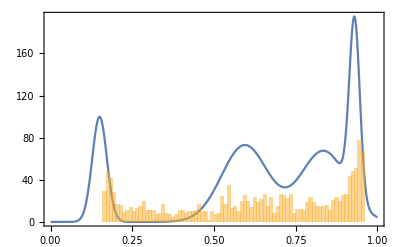
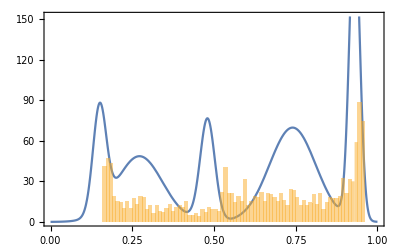
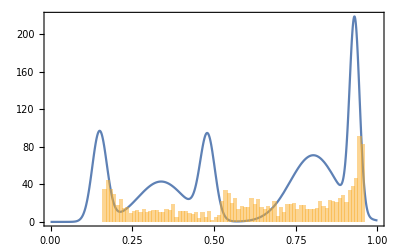
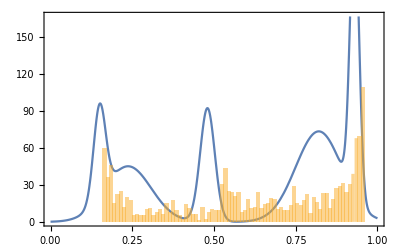
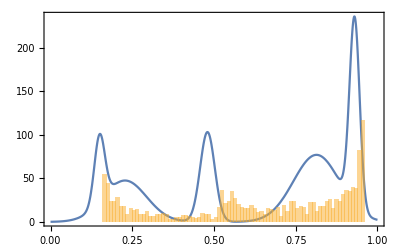
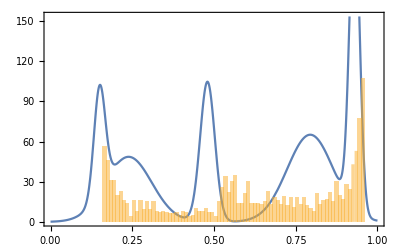
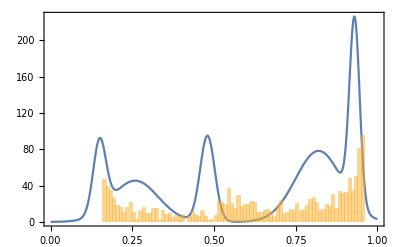
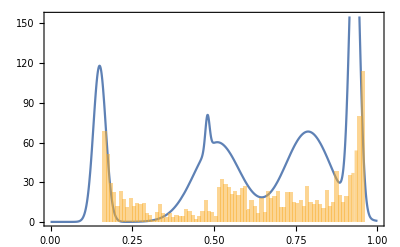

```mathematica
Table[Show[Plot[(A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2])/.fitL⟦j⟧,{xn,0,1},Frame->True],HisT2⟦j⟧],{j,1,Length[fitL]}]
```